```mathematica
g = Import["/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/adj800miss2.txt","Table"]
```

{1}
 |  |  |  |

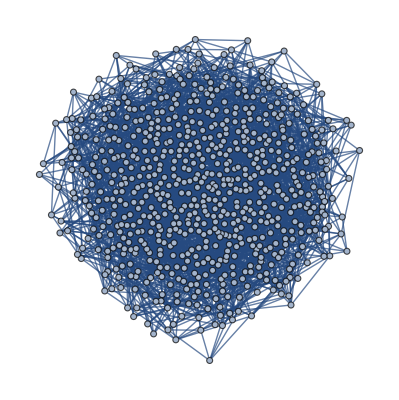

```mathematica
gnew = AdjacencyGraph[g]
```

```mathematica
FindIndependentVertexSet[gnew,800,100000][[1]]
```

{1,2,4,9,10,14,15,17,20,25,26,29,38,41,42,44,47,48,52,53,54,59,61,62,63,66,74,84,85,90,92,95,97,98,99,102,103,106,107,110,113,114,115,117,126,127,135,137,140,141,142,146,147,150,153,154,156,157,159,160,163,165,169,172,173,174,175,178,183,203,204,205,215,216,217,224,225,229,230,231,234,237,238,239,250,251,254,256,258,259,261,263,265,270,271,281,282,283,287,288,291,294,295,297,298,308,314,315,317,329,330,333,343,351,354,357,358,359,363,365,368,369,371,373,381,394,397,398,406,407,409,416,419,422,428,429,432,436,438,444,445,448,452,453,455,456,457,458,459,467,468,471,476,479,481,489,508,515,518,524,526,534,535,536,539,545,548,550,551,563,565,569,570,576,582,584,588,591,596,597,598,604,605,609,610,621,625,627,629,631,635,638,643,645,649,650,654,655,659,665,666,667,685,686,689,692,693,698,702,710,714,724,725}

```mathematica
Length[FindIndependentVertexSet[gnew,800,100000][[1]]]
```

213

```mathematica
Export["/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/maxindep800miss2",FindIndependentVertexSet[gnew,800,10000][[1]],"Table"]
```

/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/maxindep800miss2

```mathematica
Export["/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/adj800miss2",Normal[AdjacencyMatrix[gnew]],"Table"]
```

/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/adj800miss2